## Attempts with predict and classify

## Trying to use File[]

```mathematica
imagesPath = FileNameJoin[{NotebookDirectory[],"ResistorProject", "Assets", "Images"}];
dataPath = NotebookDirectory[] <> "ResistorProject/Assets/ResistorData/";
```

```mathematica
filesByType[type_?StringQ] := Map[
	File[#]->type&,
	FileNames[{"*.jpg", "*.png"}, dataPath <> type <> "/"]
];
```

```mathematica
makeData[] := Flatten @ Map[
	filesByType,
	StringDrop[
		Select[FileNames["*",dataPath], DirectoryQ],
		StringLength[dataPath]
	]
];
```

```mathematica
newBlurry[data_, n_] :=
Module[
	{toBlur},
	toBlur = RandomSample[data, n];
	toBlur/.(x_->y_):>GaussianFilter[x,15]->y
]
```

```mathematica
data = RandomSample[makeData[]];
```

```mathematica
data[[1]]
```

File[/Users/carolinadelgadillo/Documents/GitHub/WSS2017/ResistorProject/Assets/ResistorData/220000/20170629_223701.png]→220000

```mathematica
Length[data]
```

730

```mathematica
trainingData = data[[;;500]];
testData = data[[501;;]];
```

```mathematica
getAllImages[x_]:=Map[
Import[Keys[{#}][[1]]]->ToExpression[Values[{#}][[1]]]&,
x
];
```

```mathematica
trainingSet = getAllImages[trainingData];
testSet = getAllImages[testData];
```

```mathematica
trainingSet = Join[trainingSet, newBlurry[trainingSet,150 ]];
```

```mathematica
trainingSet = RandomSample[trainingSet];
```

```mathematica
newBlurry[trainingSet, 1]
```

{-Graphics-→470}

```mathematica
trainingSet[[1]]
```

-Graphics-→47000

```mathematica
cNoParameters = Classify[trainingSet, PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
img =-Graphics-;
```

```mathematica
cNoParameters[resistorLightCrop[img],"Probabilities"]
```

<|10→0.884199,22→0.011505,47→0.00407245,470→0.0866448,1000→0.00611381,2200→0.000359628,4700→0.00626333,47000→1.49014×10^-6,220000→0.000840241|>

```mathematica
mask=DeleteSmallComponents[Binarize[ColorNegate@img,0.5]];
ans = ImageRotate[ImageTrim[img,#[[1]],20],#[[2]]+Pi/2,"SameRatioCropping"]&/@ComponentMeasurements[mask,{"BoundingBox","Orientation"}][[All,2]];
```

```mathematica
ans = Blur[ans[[1,1]]]
```

-Graphics-

```mathematica
cNoParameters[ans,"Probabilities"]
```

<|10→0.000128907,22→0.000446083,47→0.0000428603,470→0.00107261,1000→0.0000234047,2200→0.322579,4700→0.000163324,47000→0.568014,220000→0.10753|>

```mathematica
ClassifierInformation[cNoParameters]
```

Classifier information
Method | Logistic regression
Number of classes | 9
Number of features | 1
Number of training examples | 650
L1 regularization coefficient | 0
L2 regularization coefficient | 10.

```mathematica
cNoParametersM = ClassifierMeasurements[cNoParameters, testSet]
```

ClassifierMeasurementsObject[…]

```mathematica
cNoParametersM["Accuracy"]
```

0.804348

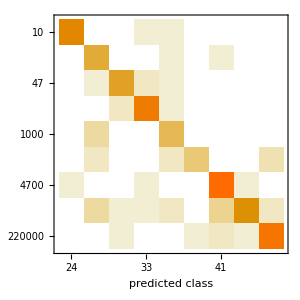

```mathematica
cNoParametersM["ConfusionMatrixPlot"]
```

```mathematica
cNeuralNet = Classify[trainingSet, Method->"NeuralNetwork", PerformanceGoal->"Quality", FeatureExtractor->"ImageFeatures"]
```

ClassifierFunction[…]

```mathematica
cNeuralNetM = ClassifierMeasurements[cNeuralNet, testSet]
```

ClassifierMeasurementsObject[…]

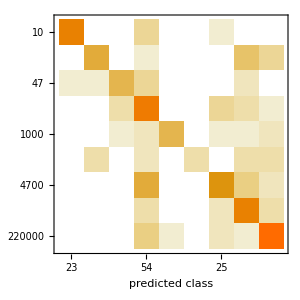

```mathematica
cNeuralNetM["ConfusionMatrixPlot"]
```

```mathematica
pNoParameters = Predict[trainingSet]
```

PredictorFunction[…]

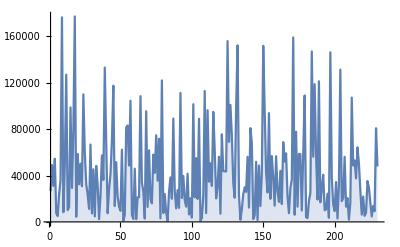

```mathematica
Show[
DiscretePlot[
Module[
{image, value},
image = Keys[testSet[[x]]];
value = Values[testSet[[x]]];
Abs[value - pNoParameters[image]]
],
{x, 1, Length[testSet], 1}
]
]
```